```mathematica
Clear["Global`*"]
```

```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=1;u0=10^-10;ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1};αSch=2.;
Vs1[r_,a_,c1_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
Vs2[r_,a_,c2_,d1_]=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r];V[r_]=-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&[r];
```

```mathematica
aa={500,50,10,3,1,0.1,0.05,0.01};
```

```mathematica
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k},
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->30,AccuracyGoal->Infinity,PrecisionGoal->20];
δr=δ/.δs;
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
```

```mathematica
hhhc1[en_,a_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc1[a_,c1_]:=N[hhhc1[10^-10,a,c1]-δ50e[10^-10,V[r]],8];
Determinec1[a_]:=Module[{aaa,findroot},aaa=a;
Print[a];findroot=FindRoot[hhhc1[10^-10,aaa,c1]==δ50e[10^-10,V[r]],{c1,-40},MaxIterations->10000,AccuracyGoal->30,PrecisionGoal->30,WorkingPrecision->80,StepMonitor:>Print[{c1,evnhhhc1[aaa,c1]}]];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
Module[{aaa,findroot},aaa=3;
Print[aaa];findroot=FindRoot[hhhc1[10^-10,aaa,c1]==δ50e[10^-10,V[r]],{c1,-25},MaxIterations->10000,AccuracyGoal->30,PrecisionGoal->30,WorkingPrecision->80,StepMonitor:>Print[{c1,evnhhhc1[aaa,c1]}]];
Print[c1/.findroot];
c1/.findroot
]
```

3

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (hhhc1[1/10000000000,3,c1]==-0.000211093309760295575157202340874) 小于 WorkingPrecision (80.).

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+0.52911363278534141488136087445530016795878249401894103400998478543437544164218041 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

{-92.123618251345340851679907311495643950505742066448076616079085488509071735593385,-0.00025407316}

{-92.681307804411410711347251002588547057668458465473310618102209153724676472293983,-0.00022593082}

{-93.085798245295514145710104900818483225701908961568684304500967224583193307044238,-0.00020143134}

{-93.77924965778840308313611742402849387176805049369902449875774243613540650696682,-0.00014812501}

{-95.444300962310066557862929085485739200897224082163619822469380501692421621956677,0.00010704785}

{-95.016971899966328582336319752258598406390400226109911255362008525558999956638393,0.000012474672}

{-94.950498796385484268987369242892847141066165874402034985289322147337809977096128,3.1436834×10^-7}

{-94.948718612150278241674327994457056837775245402575405190792944814412825197790101,-3.4979588×10^-9}

{-94.948718611657418327242578209630710667259135441662627099966471096855456714699599,-3.4979268×10^-9}

$Aborted

```mathematica
c1a[[4]]=%
```

29.179626225530775086730063508968531184223327633380074669798946756095190252671046

```mathematica
Determinec1[0.001];
```

0.001

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (hhhc1[1/10000000000,0.001,c1]==-0.000211093309760295575157202340874) 小于 WorkingPrecision (80.).

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+2539.745437369638738561459798864289606902981744587037765849268395252640108713878 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

$Aborted

```mathematica
c1a=Determinec1[#]&/@aa;
```

500

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (hhhc1[1/10000000000,500,c1]==-0.000211093309760295575157202340874) 小于 WorkingPrecision (80.).

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+0.0050794908747392775828610643947708816124043119425818339264958539401700042397649319 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

{-66.675545582802417001480272937470538909460906736160272771323063417929763857865416,-0.00039216467}

{-74.453576459918368132000598311152124352861275813814004196306602066517237617247959,-0.0002861897}

{-75.72054872953940126623364821071078842675179080651929949915279816110163457407575,-0.00025386954}

{-76.599603662164087344423862117777786890917127024525922010076144021268782829606786,-0.00022588882}

{-77.242696903628293413938112272437512079295929600193945890495887978434634029872501,-0.00020145587}

{-78.346755455727774926603669505999234151777077206661276455270465032495703414848803,-0.00014847687}

{-80.996619704968752771241097995615225324255062147437911879727799898932446626147562,0.00010264129}

{-80.358978939545765842989846327467038545852842093002934574872037948439021994878641,0.000014829787}

{-80.233135721886673917767854172164795787274389078076686864103082171596426621934454,4.095929×10^-7}

{-80.229464689747204219603840286958637522354557775362249810379368123158352571608694,8.8306652×10^-10}

{-80.229456751710034661763540758171263868929349998923182801873236124111842654119077,7.9161635×10^-15}

{-80.229456751638873684691442941286990771483372793598645177470855482307816077028676,-5.0813547×10^-20}

{-80.229456751638874140898222363829911902574730456387640701044777788673600857406541,-6.3391556×10^-23}

{-80.229456751638874141469494780251436966374903646842779992349764261227830085957247,1.5893329×10^-25}

{-80.229456751638874141468066085235627060403117496195687106471963172884348533742845,-1.1×10^-31}

{-80.229456751638874141468066086224460738161134088072658801074599716358856531553143,0.}

{-80.229456751638874141468066086221979738802399267397652327638146008745260586237477,0.}

-80.229456751638874141468066086221979738802399267397652327638146008745260586237477

50

FindRoot::precw: 参数函数的精度 (hhhc1[1/10000000000,50,c1]==-0.000211093309760295575157202340874) 小于 WorkingPrecision (80.).

{-40.135355802407130914479309000941736433504303580151051498667342143571692825851608,-0.00023025316}

{-40.232308933444929801513711332108247428848197516067799626646250413272853192579683,-0.00020483413}

{-40.348869011628164017533097790585744284366432186218262674515252167175025853426534,-0.00016717896}

{-40.576145763645410915122311367261368976879182373600071511072243088135875033341732,-0.00005710178}

{-40.632715739086806853726067431214244206401990515825000907864503013598303493848978,-0.000017359615}

{-40.655392268967201651461282123854339752869143234720495227475213442840459655197598,6.5375261×10^-7}

{-40.654598665212901112638166748346945884501681453481821454849748327265763380689625,6.0982482×10^-10}

{-40.654597921193875167971852316775408474507242943465292474327423938109815533262813,-1.8569287×10^-12}

{-40.654597923447607492217114962933792345578755882540138063661309601041120709641882,-4.5439331×10^-15}

{-40.654597923453122407339892912647104086515780353209447081965111327226220967251219,-1.1121242×10^-17}

{-40.654597923453135905010592212714947715199543399592929503416277604051908603007549,-2.7253746×10^-20}

{-40.654597923453135938087225020463719247545271819235724344503823734487405003944022,-6.7443115×10^-23}

{-40.654597923453135938169489564780505858909719932762773014065645541854730796592311,1.7165198×10^-25}

{-40.654597923453135938169280185512657879245847836275410792422986229047393794953455,-4.4075×10^-28}

{-40.654597923453135938169280721759079903174513093069030532411194280668930933311781,6.×10^-34}

{-40.654597923453135938169280721758297246183418406761603051751615883321014570081961,0.}

-40.654597923453135938169280721758297246183418406761603051751615883321014570081961

10

FindRoot::precw: 参数函数的精度 (hhhc1[1/10000000000,10,c1]==-0.000211093309760295575157202340874) 小于 WorkingPrecision (80.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

{-47.373028459794400616124600294967613069492289930932985697784341250334785184702528,-0.00052504874}

{-64.152457891918713813935974375861704902408340753436837230074503384643892089700615,-0.000092596768}

{-64.537846477256791977986060741859494600655000984024403282527731575619494263671878,0.000026580531}

{-64.471089217866659396509753833668557811162077131613220497889710002647681996334365,1.2629701×10^-6}

{-64.467601449004253297288070294778031468000487268148273811490713825967184295990408,6.1916082×10^-9}

{-64.467584223634382675646197275104466970868778406180189933636955198207375731102356,2.6661979×10^-13}

{-64.467584222892583894284463356648848869244706593990720459593946196781568047522667,-9.3896383×10^-18}

{-64.467584222892610017904225029850397444894283165022683839986959371892262746704145,1.3096296×10^-22}

{-64.467584222892610017539863162535814978598881952029503532798729756593992828776514,-1.81533×10^-27}

{-64.467584222892610017539868213102746890772867112775002996122898808098670578895011,2.×10^-32}

{-64.467584222892610017539868213033944968358558788012307092037589579343516064935542,0.}

Divide::infy: 碰到无穷表达式 1/0.

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

FindRoot::jsing: 在点 {c1} = {-64.467584222892610017539868213033944968358558788012307092037589579343516064935542} 碰到奇异雅克比. 尝试扰动初始点.

-64.467584222892610017539868213033944968358558788012307092037589579343516064935542

3

{-39.492772828787421807997977986358374081532537526750506022575463633891591846809942,0.0002647597}

{-39.020070537783068845699513976245182271354304773999320986840626732484345550570364,0.000067774595}

{-38.790726802525448552130567142760576821671849616400059757258573665660580007292535,4.4701221×10^-6}

{-38.772531830299814462466156506625805462516041421166742673867912439101623615398635,3.9420481×10^-8}

{-38.772368533250246865857843199788498918818852500728723661078819568781682723548038,4.1454474×10^-12}

{-38.772368516075948315528022449313231982990488897901232578835955348604269545198125,3.96144×10^-17}

{-38.772368516075784196152336290750549241204222519368239495344640806577666744982876,4.5935454×10^-22}

{-38.772368516075784194249266227698026988961538631378732204037306571490741213352484,5.336716×10^-27}

{-38.772368516075784194249244118047447473401480259865338765782586445929591663775605,5.×10^-32}

{-38.772368516075784194249244117841445702374251555397179742671606821511915070671357,0.}

Divide::infy: 碰到无穷表达式 1/0.

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

FindRoot::jsing: 在点 {c1} = {-38.772368516075784194249244117841445702374251555397179742671606821511915070671357} 碰到奇异雅克比. 尝试扰动初始点.

-38.772368516075784194249244117841445702374251555397179742671606821511915070671357

1

{-39.999999999942568807318340255382445429020421763612272900253331032797762528253512,-0.00027957551}

{-41.050078508724537162349710248099042951949377883355294208020934094901589644148305,-0.00024406493}

{-41.675649823658812419692034927250041663140392200470576335340315975659093533983171,-0.00021718278}

{-42.143263516959324516871420002235718492006698542368572345128555200394932416948238,-0.00019322102}

{-43.180157546646464022297888597687618357834158695273033947171190680513896626507322,-0.00012274534}

{-44.651891350177188417529979400627969376922727200863200833930287129418244556338105,0.000058140109}

{-44.331573648314775504910733502597863871227775624358618774579305150402942217627877,5.4794752×10^-6}

{-44.294769002140300899309927678933833821250295982971602672032826639533635129941404,5.6493248×10^-8}

{-44.294383750522138505301661797623870817208551468003402931136424119758532963225652,3.4192674×10^-10}

{-44.294381363248460451944392261324947323867062398158502441900708118330145237916265,-6.8952442×10^-12}

{-44.294381410552481478004106459789960122572233702206571125103313810135968284259586,3.0155782×10^-16}

{-44.294381410550412836109943496812090738691587715136040103975776003144210406316519,3.3351729×10^-21}

{-44.294381410550412813231153093243382023776047624436622765231907839086248321271454,3.692211×10^-26}

{-44.294381410550412813230899808950904319194655990131225829610868393040194984391042,-1.8×10^-31}

{-44.294381410550412813230899810215126403928959720128337470969701874779849690092111,0.}

Divide::infy: 碰到无穷表达式 1/0.

General::stop: 在本次计算中，Divide::infy 的进一步输出将被抑制.

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

General::stop: 在本次计算中，Infinity::indet 的进一步输出将被抑制.

FindRoot::jsing: 在点 {c1} = {-44.294381410550412813230899810215126403928959720128337470969701874779849690092111} 碰到奇异雅克比. 尝试扰动初始点.

General::stop: 在本次计算中，FindRoot::jsing 的进一步输出将被抑制.

-44.294381410550412813230899810215126403928959720128337470969701874779849690092111

0.1

{-67.555553376118850160605348176384237120373454844909689156582075901339786118943213,-0.0003319641}

{-74.068234105623348003750682226501620889832116027695882916881669266670630186246917,-0.00024617387}

{-75.332897953825830649839064449973528533112211518557671966000019452285845767200183,-0.0002190435}

{-76.261197720579900233556205136152589074852769090325532689464718060645491011902445,-0.00019531009}

{-78.210036804365515955947660296954123051260874054697957936876502544479609605093934,-0.00013036797}

{-81.372404297295445903203009445763311461241032614889419928302735487477005654354635,0.000060289894}

{-80.707611330329613030330000579612895429221679822403778672249081683367489076951631,5.8667694×10^-6}

{-80.628401982189054845178764934466115485278366731709344091086100224896772399834283,6.588613×10^-8}

{-80.627761562097343967719477750871258089728872462102676385948904407091360295513657,1.9515835×10^-8}

{-80.627492129346140388034518348193015798247024603058293731616728916873260918140671,1.0107641×10^-11}

{-80.627491989721660827770251009594806468582044063676541918771882054369792038896586,1.1453721×10^-16}

{-80.627491989720083453372623359182206376906127219928456813144053632647516186499117,-1.3069177×10^-18}

{-80.627491989720083453371580377554155457285953947211183994499386558520111182976898,-1.3069177×10^-18}

-80.627491989720083453371580377554155457285953947211183994499386558520111182976898

0.05

{-39.999999988759506727777179924252735693096882646314332839900965693076144206371726,-0.00046060651}

{-147.03749816324597660773468754972988930370240234900791587196774723637729139015112,-0.00029477317}

{-150.26314780684316502481077132821482253364763264580422546454168119979495756464214,-0.00026016974}

{-152.32905758777584831031934646159097639858597309998275158954413721251937778159223,-0.00023089164}

{-153.77647861123676632394658725276952795708076793650685189264874538976411891394701,-0.00020558372}

{-155.26149526646347644580268019571157662923891657653793239046456822946180688089392,-0.00017399615}

{-158.29690760465515992768488955164496309492868176056989738327818046903301484637207,-0.000081648059}

{-160.3744206978026793991828045886774900638224372251908054850425796879870164710009,0.000019908595}

{-160.04737059723256216083371093027198627871019142669558068964946823803934836801957,7.2384421×10^-7}

{-160.03455199522564383522321751067212223938220778346846605512183175697752947533261,1.0610857×10^-9}

{-160.03453314947333064131100416554896751680890765646799607197980784336471144995994,3.9243298×10^-13}

{-160.03453314249171175973622050072223477167560376915963702248722579899946862194669,2.4894526×10^-18}

{-160.03453314249166530035446036310685508371788772887866889686287131170570423894274,-2.6618735×10^-20}

{-160.03453314249166530035443007043409401458898219870985850465384785825922209906625,-2.6618735×10^-20}

-160.03453314249166530035443007043409401458898219870985850465384785825922209906625

0.01

{-450.,-0.00046130345}

{-725.93479285871451083436647828080990127226816469144073979803544290055750645814977,-0.0004446712}

{-918.88028465575534112813542137967803003229725599740379309271091667043395847142739,-0.00024316873}

{-921.8799817593270712688949649562340977919318666338258281664239350287365401584794,-0.00021599891}

{-924.01406620881660150136361593926854582358433929953611159478984002603839335094283,-0.00019242754}

{-926.85469017114511172811871808985363947731839520371413747130359810052665229674052,-0.00015345812}

{-936.68005735687353514200740569032864457911074464262629231826814293663414546710993,0.00014048606}

{-934.22779631746253863758456072553657218411675067553434694775922484604175843557669,0.000026078562}

{-933.54214929322321488097757481302587983770945661059071835652236647788572503732116,1.3300922×10^-6}

{-933.50338121404963271680839045566852316624862643836541595262579476926266115392258,3.6659588×10^-9}

{-933.5032747476052792290808306968109929983550487918493975421110401775498600894305,3.3631978×10^-11}

{-933.50327375674849659121039730094233805813518477454889830461673699982997981507487,-1.1591992×10^-13}

{-933.50327376014171901112327522747049032043121089757079253797999592893874002041761,3.7366583×10^-18}

{-933.50327376014156790622233638340605693312280016309139227573297118122459848826563,-6.0509126×10^-18}

{-933.50327376014156790622202886097658059321207750584210792419817082599896743430302,-6.0509126×10^-18}

-933.50327376014156790622202886097658059321207750584210792419817082599896743430302

```mathematica
δ50[V_]:=Module[{en,len},
len=Length@ee;
Table[
en=ee[[i]];
δ50e[en,V],{i,1,len}]
]
```

```mathematica
δa=Table[δ50[Vs1[r,aa[[n]],c1a[[n]]]],{n,Length@aa}];
Δa=Abs[δa[[#]]-δ50[V[r]]]&/@Range@Length[aa];
La=Transpose@({ee}~Join~{Δa[[#]]})&/@Range@Length[aa];
```

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+0.01018811983638097961517073791701367074250972341277676335817676268167538222534934 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/100000+0.01018811983638097961517073791701367074250972341277676335817676268167538222534934 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+0.01018811983638097961517073791701367074250972341277676335817676268167538222534934 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.21648) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-2.50987) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==0.585276) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/10000000000]==1,u[1/10000000000]==1/10000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.616853) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-15.5631) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==0.0432091) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

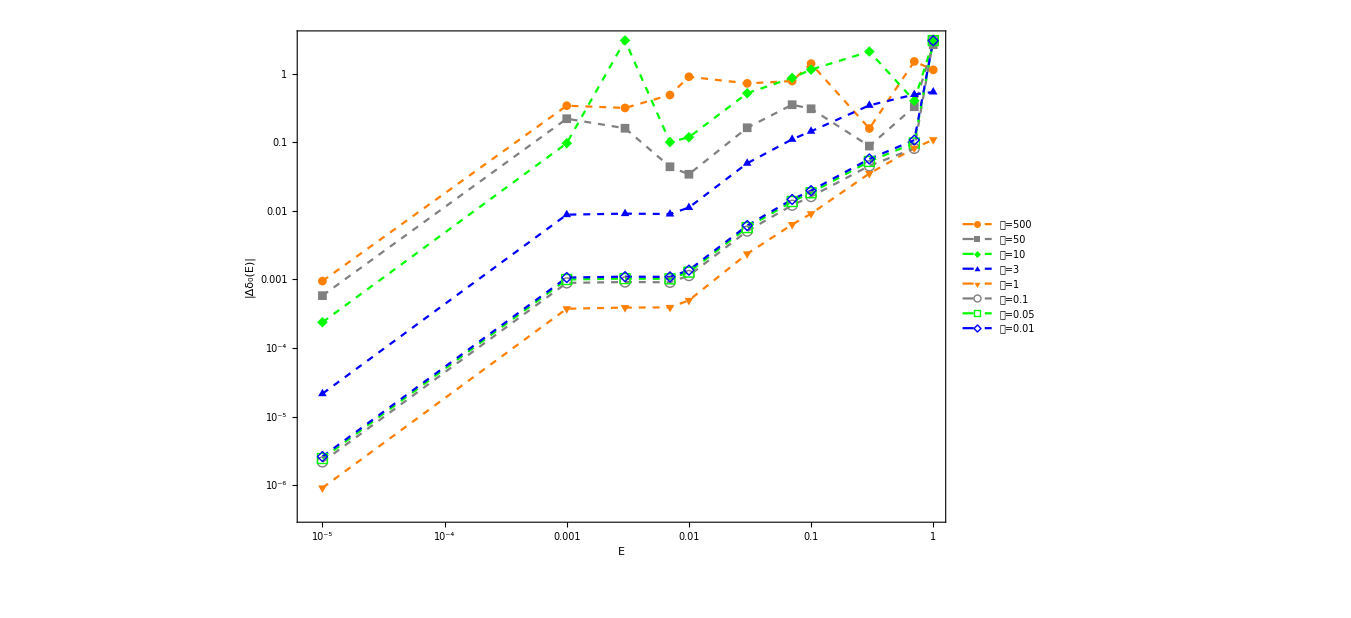

```mathematica
ListLogLogPlot[Table[Drop[La[[n]],1],{n,Length@aa}],Frame->True,Joined->True,PlotMarkers->Automatic,ImageSize->1000,FrameLabel->{"E","|Δδ_0(E)|"},RotateLabel->False,PlotStyle->{{Dashed,Orange},{Dashed,Gray},{Dashed,Green},{Dashed,Blue}},PlotLegends->(("𝒶="<>ToString[#])&/@aa)]
Export["C:\\Users\\ASUS\\OneDrive\\文档\\Test_6\\Test_PhaseShift_Various_a.eps",%];
```